```mathematica
t=0.33;
```

```mathematica
notes={0,0,0,2,4,2,0,4,2,2,0}-6;durées={t,t,t,t,2t,2t,t,t,t,t,4t};timbres={z,z,z,z,z,z,z,z,z,z,z};
```

```mathematica
melodie=Transpose[{notes,durées}]
```

{{-6,0.33},{-6,0.33},{-6,0.33},{-4,0.33},{-2,0.66},{-4,0.66},{-6,0.33},{-2,0.33},{-4,0.33},{-4,0.33},{-6,1.32}}

```mathematica
m=SoundNote@@@melodie/.t->0.33
```

{SoundNote[-6,0.33],SoundNote[-6,0.33],SoundNote[-6,0.33],SoundNote[-4,0.33],SoundNote[-2,0.66],SoundNote[-4,0.66],SoundNote[-6,0.33],SoundNote[-2,0.33],SoundNote[-4,0.33],SoundNote[-4,0.33],SoundNote[-6,1.32]}

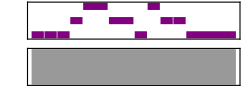

```mathematica
Sound[m]
```

```mathematica
Sound[SoundNote@@@Transpose[{notes+7,durées}]/.t->0.33]
```

-Graphics-

```mathematica
Transpose[{notes,notes+7}]
```

{{-6,1},{-6,1},{-6,1},{-4,3},{-2,5},{-4,3},{-6,1},{-2,5},{-4,3},{-4,3},{-6,1}}

```mathematica
Sound[SoundNote@@@Transpose[Transpose[{Reverse[notes],durées}]]/.t->0.33]
```

Sound[{SoundNote[-6,-4,-4,-2,-6,-4,-2,-4,-6,-6,-6],SoundNote[0.33,0.33,0.33,0.33,0.66,0.66,0.33,0.33,0.33,0.33,1.32]}]

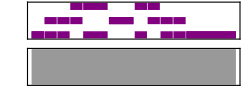

```mathematica
Sound[SoundNote@@@Transpose[{Transpose[{notes,Reverse[notes]}],durées}]/.t->0.33]
```

```mathematica
1-Log[2]//N
```

0.306853

```mathematica
Transpose[{notes,Reverse[notes]}]
```

{{{9,16},{7,14}},{{10,17},{9,16}},{{14,21},{10,17}},{{12,19},{9,16}},{{10,17},{7,14}},{{9,16},{5,12}},{{7,14},{0,7}},{{0,7},{7,14}},{{5,12},{9,16}},{{7,14},{10,17}},{{9,16},{12,19}},{{10,17},{14,21}},{{9,16},{10,17}},{{7,14},{9,16}}}

```mathematica
SoundNote@@@Transpose[{Transpose[{notes,Reverse[notes]}],durées,timbres}]
```

{SoundNote[{-6,-6},t,z],SoundNote[{-6,-4},t,z],SoundNote[{-6,-4},t,z],SoundNote[{-4,-2},t,z],SoundNote[{-2,-6},2 t,z],SoundNote[{-4,-4},2 t,z],SoundNote[{-6,-2},t,z],SoundNote[{-2,-4},t,z],SoundNote[{-4,-6},t,z],SoundNote[{-4,-6},t,z],SoundNote[{-6,-6},4 t,z]}

```mathematica
Transpose[{Transpose[{notes,Reverse[notes]}],durées,timbres}]
```

Transpose::nmtx: The first two levels of the one-dimensional list {{{-6, -6}, {-6, -4}, {-6, -4}, {-4, -2}, {-2, -6}, {-4, -4}, {-6, -2}, {-2, -4}, {-4, -6}, {-4, -6}, « 1 »}, {t, t, t, t, 2\ t, 2\ t, t, t, t, t, « 1 »}, {z, z, z, z, z, z, z, z, z, z, « 4 »}} cannot be transposed.

Transpose[{{{-6,-6},{-6,-4},{-6,-4},{-4,-2},{-2,-6},{-4,-4},{-6,-2},{-2,-4},{-4,-6},{-4,-6},{-6,-6}},{t,t,t,t,2 t,2 t,t,t,t,t,4 t},{z,z,z,z,z,z,z,z,z,z,z,z,z,z}}]

```mathematica
Transpose[{notes,durées,timbres}]
```

{{-6,t,z},{-6,t,z},{-6,t,z},{-4,t,z},{-2,2 t,z},{-4,2 t,z},{-6,t,z},{-2,t,z},{-4,t,z},{-4,t,z},{-6,4 t,z}}

```mathematica
Transpose[{notes,Reverse[notes]}]
```

{{-6,-6},{-6,-4},{-6,-4},{-4,-2},{-2,-6},{-4,-4},{-6,-2},{-2,-4},{-4,-6},{-4,-6},{-6,-6}}